```mathematica
<<Local`QFTToolKit2`
```

Thu 30 May 2019 08:06:14

### Charged Black Holes

#### Black hoes with electric charge

```mathematica
PR["Reissner-Nordstrom metric",
NL,e[2.1]=$={$ds=d[s]^2->-A[r] d[t]^2+d[r]^2/A[r]+r^2 d[Ω]^2,

$sA0=A[rr_]:>(((1-Subscript[r, "+"]/rr)(1-Subscript[r, "-"]/rr))),
$sA=A[rr_]:>(((1-Subscript[r, "+"]/rr)(1-Subscript[r, "-"]/rr))/.$rpm),
$rpm0=Subscript[r, pm]->G M (1+pm[√(1-Q^2/Sqrt[G M^2])]);
$rpm={$rpm0/.pmDn,$rpm0/.pmUp},
$ds1=$ds/.$sA//Collect[#,d[_],Simplify]&

};(ColumnForms[#1,4]&)[$],CG["e[2.1]"]
]
```

Reissner-Nordstrom metric
d[s]^2→d[r]^2/A[r]-A[r] d[t]^2+r^2 d[Ω]^2
A[rr_]:>(1-(r_+)/rr) (1-(r_-)/rr)
A[rr_]:>((1-(r_+)/rr) (1-(r_-)/rr)/.$rpm)
r_-→G M (1-√(1-Q^2/(√(G M^2))))
r_+→G M (1+√(1-Q^2/(√(G M^2))))
d[s]^2→(r^2 d[r]^2)/(G √(G M^2) Q^2-2 G M r+r^2)-((G √(G M^2) Q^2-2 G M r+r^2) d[t]^2)/r^2+r^2 d[Ω]^2e[2.1]

A[r]→1+(M Q^2)/r^2-(2 M)/r

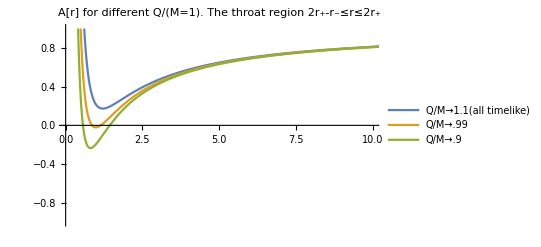

```mathematica
$sAr=A[r]->(A[r]/.$sA/.G->1)//Expand//PowerExpand
Plot[{$sAr[[2]]/.{M->1,Q->1.1},$sAr[[2]]/.{M->1,Q->.99},$sAr[[2]]/.{M->1,Q->.9}},{r,0,40},PlotLegends->{"Q/M→1.1(all timelike)","Q/M→.99","Q/M→.9"},PlotLabel->"A[r] for different Q/(M=1).\nThe throat region 2r_(<+>)-r_(<->)≤r≤2r_(<+>)",PlotRange->{{0,10},{-1,1}}]
```

#### Exercise 1

```mathematica
PR[CO["Exercise 1. Show that a photon moving in a radial direction in a subextremal Reissner-Nordstrom black hole follows a path determined by ",tuDPartial[t,r]->pm[r^2/((r-Subscript[r, "+"])(r-Subscript[r, "-"]))]],
line,NL,"The RN metric: ",$=e[2.1][[1]]/.e[2.1][[2]],
NL,"In the radial case for a photon ",$s={d[Ω]->0,d[s]->0},
Yield,$=$/.$s,
Yield,$=tuRuleSolve[$,d[r]],
Imply,$vel=$=#/d[t]&/@#&/@$//tuOpGather[Sqrt]//Simplify//PowerExpand,
NL,"Apparently the velocity ",$[[1,1]]->0," at ",r->{Subscript[r, "-"],Subscript[r, "+"]},
NL,"● The accelerations ",
$1=tuDPartial[$[[1,2]],t],"POFF",
Yield,$1=$1//tuDerivativeExpand[{Subscript[r, "-"],Subscript[r, "+"]}],
Yield,$s=tuDPartial[r,t]->$[[1,2]],"PON",
Yield,$accel=$1=tuDPartial[$s[[1]],t]->($1/.$s//Simplify),

NL,"● Integrating the inverse velocity",
Yield,$=1/#&/@$[[2]]/.d[t]/d[r]->tuDPartial[t,r];Yield,$=xIntegral[#,r]&/@$,
Yield,$[[2]]=$[[2]]//tuOpIndependentVarActivate[]//tuOpGather[Log];
$[[1]]=t;$//Framed
]
```

Exercise 1. Show that a photon moving in a radial direction in a subextremal Reissner-Nordstrom black hole follows a path determined by UnderBar[∂]_r[t]→±[r^2/((r-r_-) (r-r_+))]
————————————————————————————————————————————————————————————
The RN metric: d[s]^2→r^2 d[Ω]^2+d[r]^2/((1-(r_-)/r) (1-(r_+)/r))-d[t]^2 (1-(r_-)/r) (1-(r_+)/r)
In the radial case for a photon {d[Ω]→0,d[s]→0}
→ 0→d[r]^2/((1-(r_-)/r) (1-(r_+)/r))-d[t]^2 (1-(r_-)/r) (1-(r_+)/r)
→ {d[r]→-(d[t] √(r-r_-) √(1-(r_-)/r) √(r-r_+) √(1-(r_+)/r))/r,d[r]→(d[t] √(r-r_-) √(1-(r_-)/r) √(r-r_+) √(1-(r_+)/r))/r}
⇒ {d[r]/d[t]→-((r-r_-) (r-r_+))/r^2,d[r]/d[t]→((r-r_-) (r-r_+))/r^2}
Apparently the velocity d[r]/d[t]→0 at r→{r_-,r_+}
● The accelerations UnderBar[∂]_t[-((r-r_-) (r-r_+))/r^2]
→ UnderBar[∂]_t[UnderBar[∂]_t[r]]→((r-r_-) (r-r_+) (r_- (r-2 r_+)+r r_+))/r^5
● Integrating the inverse velocity
→ 
→ UnderBar[∂]_r[t]r→r^2/((r-r_-) (r-r_+))r
→ t→r+Log[(r-r_-)^((r_-^2)/(r_--r_+)) (r-r_+)^(-(r_+^2)/(r_--r_+))]

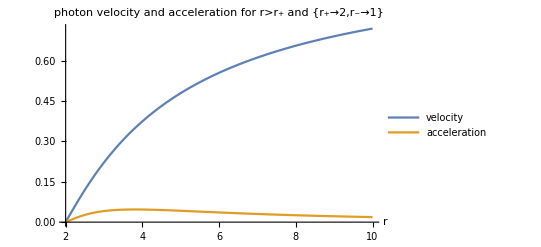

```mathematica
$vel;
Plot[{ $vel[[2,2]]/.{Subscript[r, "+"]->2,Subscript[r, "-"]->1},$accel[[2]] /.{Subscript[r, "+"]->2,Subscript[r, "-"]->1}},{r,2,10},PlotLegends->{"velocity","acceleration"},
PlotLabel->"photon velocity and acceleration\nfor r>r_(<+>) and {r_(<+>)→2,r_(<->)→1}",AxesLabel->Automatic]
```